```mathematica
xy[t_,r_,p_]:=r{Cos[t+p],Sin[t+p]}
```

```mathematica
xy[Pi/6,2,Pi/2]
```

xy[π/6,2,π/2]

```mathematica
Mod[.28,.04]
```

```mathematica
Head[6/10]
```

```mathematica
Clear[euclid];
euclid[a_Real,b_Real]:=euclid[Rationalize[a],Rationalize[b]];
euclid[a_,b_]:=If[b==0,a,euclid[b,Mod[a,b]]];
euclid[a_,b_,c__]:=euclid[euclid[a,b],c]
```

```mathematica
euclid[.32,.6,.5]
```

```mathematica
lcm[a_]:=a;
lcm[a_,b__]:=With[{gcd=euclid[a,b]},
gcd*LCM@@(Rationalize/@({a,b}/gcd))]
```

```mathematica
lcm[.5,.6]
```

3

```mathematica
rToR[a_,b_,c_]:={1,b/a,c/a}
```

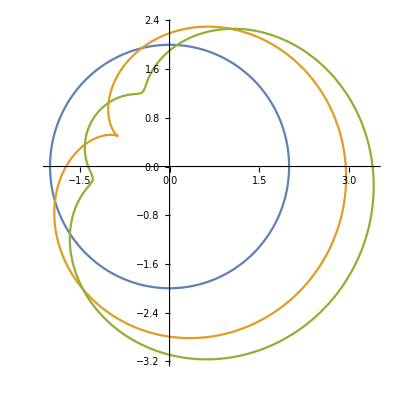

```mathematica
Module[{
s1=1,
r1=2,
p1=0,
s2=2,
r2=1,
p2=Pi/6,
s3=3,
r3=0.5,
p3=Pi/3},
ParametricPlot[{xy[s1*t,r1,p1],xy[s1*t,r1,p1]+xy[s2*t,r2,p2],xy[s1*t,r1,p1]+xy[s2*t,r2,p2]+xy[s3*t,r3,p3]},{t,0,2 Pi*lcm[1/s1,1/s2,1/s3]}]]
```

```mathematica
1/{1,2,3}
```

{1,1/2,1/3}

```mathematica
Clear[plotPtolemy];
plotPtolemy[th_,args__]:=With[{srlist=Partition[{args},4]},
With[{ss=First/@srlist,
ps=#[[3]]&/@srlist,
qs=#[[4]]&/@srlist},
ParametricPlot[Plus@@(xy[#1*t,#2,#3]&@@@srlist),
{t,0,2 Pi*lcm@@(1/ss)},ImageSize->Large,Axes->False,
ColorFunction->Function[{x,y,t},RGBColor@@((Mod[#,2 Pi]&/@(ss*{t,t,t}+qs))/(2 Pi))],
PlotStyle->Thickness[th],Background->Black
]]]
```

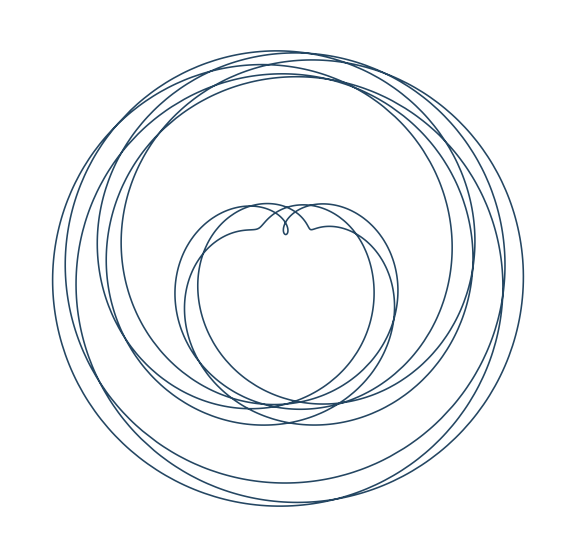

```mathematica
plotPtolemy[.002,1.8,20,0,2.4,13,Pi/6,3.8,2,Pi/6]
```

```mathematica
ListAnimate[Table[plotPtolemy[u,1.8,20,2.4,13,3.8,2],{u,0.005,1,.005}]]
```

```mathematica
0
```

```mathematica
Manipulate[plotPtolemy[th,1,r1,p1,q1,b/a,r2,p2,q2,c/a,r3,p3,q3],
{{a,1},0,20},{r1,0,20,0.1},{p1,0,2 Pi},{q1,0,2 Pi},
{{b,1},0,20},{r2,0,20,0.1},{p2,0,2 Pi},{q2,0,2 Pi},
{{c,1},0,20},{r3,0,20,0.1},{p3,0,2 Pi},{q3,0,2 Pi},
{{th,.001},.001,.02}]
```

Part::partw: Part 4 of {1,0,0} does not exist.

Part::partw: Part 4 of {0,1,0} does not exist.

Part::partw: Part 4 of {0,0,1} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

ParametricPlot::plln: Limiting value 2 π If[Indeterminate==0,ComplexInfinity,euclid[Indeterminate,Mod[ComplexInfinity,Indeterminate]]] LCM[ComplexInfinity,ComplexInfinity,ComplexInfinity,1/If[Indeterminate==0,ComplexInfinity,euclid[Indeterminate,Mod[ComplexInfinity,Indeterminate]]]] in {t,0,2 π lcm@@1/{1,0,0,0}} is not a machine-sized real number.

Part::partw: Part 4 of {1,0,0} does not exist.

Part::partw: Part 4 of {0,0.3125,0} does not exist.

Part::partw: Part 4 of {0,0,0.3125} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

ParametricPlot::plln: Limiting value 2 π If[Indeterminate==0,ComplexInfinity,euclid[Indeterminate,Mod[ComplexInfinity,Indeterminate]]] LCM[ComplexInfinity,ComplexInfinity,ComplexInfinity,1/If[Indeterminate==0,ComplexInfinity,euclid[Indeterminate,Mod[ComplexInfinity,Indeterminate]]]] in {t,0,2 π lcm@@1/{1,0,0,0}} is not a machine-sized real number.

Part::partw: Part 4 of {1,0,0} does not exist.

Part::partw: Part 4 of {0,1.53125,0} does not exist.

Part::partw: Part 4 of {0,0,0.3125} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

ParametricPlot::plln: Limiting value 2 π If[Indeterminate==0,ComplexInfinity,euclid[Indeterminate,Mod[ComplexInfinity,Indeterminate]]] LCM[ComplexInfinity,ComplexInfinity,ComplexInfinity,1/If[Indeterminate==0,ComplexInfinity,euclid[Indeterminate,Mod[ComplexInfinity,Indeterminate]]]] in {t,0,2 π lcm@@1/{1,0,0,0}} is not a machine-sized real number.

Part::partw: Part 4 of {1,15.3,0} does not exist.

Part::partw: Part 4 of {0,1.53125,0} does not exist.

Part::partw: Part 4 of {0,0,0.3125} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

ParametricPlot::plln: Limiting value 2 π If[Indeterminate==0,ComplexInfinity,euclid[Indeterminate,Mod[ComplexInfinity,Indeterminate]]] LCM[ComplexInfinity,ComplexInfinity,ComplexInfinity,1/If[Indeterminate==0,ComplexInfinity,euclid[Indeterminate,Mod[ComplexInfinity,Indeterminate]]]] in {t,0,2 π lcm@@1/{1,0,0,0}} is not a machine-sized real number.

Part::partw: Part 4 of {1,15.3,0} does not exist.

Part::partw: Part 4 of {0,1.53125,8.4} does not exist.

Part::partw: Part 4 of {0,0,0.3125} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

ParametricPlot::plln: Limiting value 2 π If[Indeterminate==0,ComplexInfinity,euclid[Indeterminate,Mod[ComplexInfinity,Indeterminate]]] LCM[ComplexInfinity,ComplexInfinity,ComplexInfinity,1/If[Indeterminate==0,ComplexInfinity,euclid[Indeterminate,Mod[ComplexInfinity,Indeterminate]]]] in {t,0,2 π lcm@@1/{1,0,0,0}} is not a machine-sized real number.

Part::partw: Part 4 of {1,15.3,0} does not exist.

Part::partw: Part 4 of {0,1.53125,8.4} does not exist.

Part::partw: Part 4 of {0,0,0.3125} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

ParametricPlot::plln: Limiting value 2 π If[Mod[If[Indeterminate==0,ComplexInfinity,euclid[Indeterminate,Mod[ComplexInfinity,Indeterminate]]],0.2]==0,0.2,euclid[Mod[If[Indeterminate==0,ComplexInfinity,euclid[Indeterminate,Mod[ComplexInfinity,Indeterminate]]],0.2],Mod[0.2,Mod[If[«1»],0.2]]]] LCM[ComplexInfinity,ComplexInfinity,1/(5 If[Mod[If[«3»],1/5]==0,1/5,euclid[Mod[If[«3»],1/5],Mod[1/5,Mod[«2»]]]]),1/If[Mod[If[Equal[«2»],ComplexInfinity,euclid[«2»]],1/5]==0,1/5,euclid[Mod[If[Equal[«2»],ComplexInfinity,euclid[«2»]],1/5],Mod[1/5,Mod[If[«3»],1/5]]]]] in {t,0,2 π lcm@@1/{1,0,0,5.}} is not a machine-sized real number.

Part::partw: Part 4 of {1,15.3,0} does not exist.

Part::partw: Part 4 of {0,1.53125,8.4} does not exist.

Part::partw: Part 4 of {0,0,3.71875} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

ParametricPlot::plln: Limiting value 2 π If[Mod[If[Indeterminate==0,ComplexInfinity,euclid[Indeterminate,Mod[ComplexInfinity,Indeterminate]]],0.2]==0,0.2,euclid[Mod[If[Indeterminate==0,ComplexInfinity,euclid[Indeterminate,Mod[ComplexInfinity,Indeterminate]]],0.2],Mod[0.2,Mod[If[«1»],0.2]]]] LCM[ComplexInfinity,ComplexInfinity,1/(5 If[Mod[If[«3»],1/5]==0,1/5,euclid[Mod[If[«3»],1/5],Mod[1/5,Mod[«2»]]]]),1/If[Mod[If[Equal[«2»],ComplexInfinity,euclid[«2»]],1/5]==0,1/5,euclid[Mod[If[Equal[«2»],ComplexInfinity,euclid[«2»]],1/5],Mod[1/5,Mod[If[«3»],1/5]]]]] in {t,0,2 π lcm@@1/{1,0,0,5.}} is not a machine-sized real number.